# Signal for the Speckle Experiment

```mathematica
(* Force the notebook to autosave after running each cell *)
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

## Retrieving Balmer-α Lines

Mathematica has the really cool feature of allowing one to look up the atomic transition data for any element. No copy/pasting from the NIST atomic spectrum database required!

```mathematica
(* Retrieve atomic transitions present in the Balmer α line *)
balmerα =SpectralLineData[EntityClass["AtomicLine",{"Hydrogen",1}],{Quantity[600,"Nanometers"],Quantity[700,"Nanometers"]}][[1;;4]]
```

{H: (3d^1)^2D_(3/2) ⟶ (2p^1)^2P_(1/2),H: (3p^1)^2P_(1/2) ⟶ (2s^1)^2S_(1/2),H: (3p^1)^2P_(3/2) ⟶ (2s^1)^2S_(1/2),H: (3d^1)^2D_(5/2) ⟶ (2p^1)^2P_(3/2)}

## Spectrum with No Inhomogenous Broadening

The line profiles will have a Lorentzian shape when considering only natural broadening. From Loudon eq. 2.5.20, this is given by

F_nat(ω) = (γ_sp/π)/((ω_0-ω)^2+γ_sp^2)

where 2 γ_sp=A_ji=1/τ_R with γ_sp≡ the radiative decay width, A_ji≡ the Einstein A coefficient, and τ_R≡ the radiative decay lifetime. To determine the radiant power of emission of each line, we simply multiply the transition probability (A_ji) by the number of atoms in state j = n_j V (n_jbeing the number density of atoms in state j, and V being the volume of the gas) and the energy of the emitted photon ℏω_ji:

Φ_E=A_ji ℏω_ji n_j V

Note that this is only valid for a diffuse gas where reabsorption is negligible. Mathematica can give us the Einstein A coefficients and the frequencies for each transition:

```mathematica
(* Get the frequency of photons emitted from each transition *)
lineFreq = SpectralLineData[balmerα,"Frequency"]
lineFreqTHz = QuantityMagnitude[lineFreq];
(* Convert to angular frequency for consistency with Loudon *)
lineω = 2*π*lineFreq
lineωTHz = QuantityMagnitude[lineω];
(* Get transition probabilities *)
lineProb = SpectralLineData[balmerα,"TransitionProbability"] 
lineProbTHz = QuantityMagnitude[UnitConvert[lineProb,"Terahertz"]];
```

{456.812 THz,456.808 THz,456.811 THz,456.802 THz}

{2870.23 THz,2870.21 THz,2870.23 THz,2870.17 THz}

{5.3877×10^7 per second,2.2449×10^7 per second,2.2448×10^7 per second,6.4651×10^7 per second}

What we don’t know yet is the number of atoms in each state. If the system is in thermal equilibrium, this can be acquired through the Boltzmann distribution such that

n_j(T) = (n_t g_j e^(-E_j/(k_B T)))/(Z(T))

where n_j≡ the number density of atoms in state j, n_t≡ the total number density of atoms, g_j≡ the statistical weight of state j = 2J+1, k_B≡Boltzmann’s constant, T≡ temperature, and Z(T) is the partition function for the system. Hence, the scaled lineshape can be written as

f_(nat,ji)(ω,T) = Φ_(E,ji)(T)F_(nat,ji)(ω) = (A_ji ℏω_ji n_t g_j e^(-E_j/(k_B T)))/(Z(T))(γ_sp/π)/((ω_ji-ω)^2+γ_sp^2)

and the unbroadened shape of the Balmer-α line with K transitions can be given by

f_(nat,Hα)(ω,T) = ∑_(m=1)^M Φ_(E,ji,m)(T)F_(nat,ji,m)(ω) =ℏn_t/(Z(T))∑_(m=1)^M A_(ji,m)ω_(ji,m)g_(j,m)e^(-E_(j,m)/(k_B T))(γ_(sp,m)/π)/((ω_(ji,m)-ω)^2+(γ_(sp,m))^2).

Since ∫_(-∞)^∞ F_L(ω)ⅆω=1, (where L signifies a Lorentzian lineshape) we can normalize equation (DisplayFormulaNumbered) to get

F_(nat,Hα)(ω,T) = 1/(R(T))∑_(m=1)^M g_(j,m)ω_(ji,m)A_(ji,m)e^(-E_(j,m)/(k_B T))(γ_(sp,m)/π)/((ω_(ji,m)-ω)^2+(γ_(sp,m))^2)

where

R(T) = ∑_(m=1)^M g_(j,m)ω_(ji,m)A_(ji,m)e^(-E_(j,m)/(k_B T)).

We can now plot equation (DisplayFormulaNumbered) to see the lineshape for the unbroadened Hα line.

```mathematica
(* get initial and final states *)
lineInitialState = SpectralLineData[balmerα,"UpperLevel"]
lineFinalState = SpectralLineData[balmerα,"LowerLevel"]
```

{H: (3d^1)^2D_(3/2),H: (3p^1)^2P_(1/2),H: (3p^1)^2P_(3/2),H: (3d^1)^2D_(5/2)}

{H: (2p^1)^2P_(1/2),H: (2s^1)^2S_(1/2),H: (2s^1)^2S_(1/2),H: (2p^1)^2P_(3/2)}

```mathematica
(* get the weight of each initial state *)
initialStateJ = SpectralLineData[lineInitialState,"JValue"]
initialStateWeight = 2*initialStateJ + 1
```

{3/2,1/2,3/2,5/2}

{4,2,4,6}

```mathematica
(* get the excitation energies of each initial state in eV *)
initialStateE = SpectralLineData[lineInitialState,"Energy"]
initialStateEeV = QuantityMagnitude[initialStateE];
```

{12.0875 eV,12.0875 eV,12.0875 eV,12.0875 eV}

```mathematica
(* function for the normalized unbroadened Balmer-α lineshape *)
kb = QuantityMagnitude[UnitConvert[Quantity[, "BoltzmannConstant"],"eV/Kelvins"]];
coeffHα[T_]:=lineProbTHz*lineωTHz*initialStateWeight*Exp[-initialStateEeV/(kb*T)];
normR[T_]:= Total[coeffHα[T]];
γsp = lineProb/2;
lorentzHα[ω_]:=(γspTHz/π)/((lineωTHz-ω)^2+γspTHz^2);
nFHα[ω_,T_]:=Total[coeffHα[T]*lorentzHα[ω]]/normR[T]

(* "Units" version of calculation lets Mathematica handle unit conversion. This is very slow, so I'm only using it as a double check. *)
coeffHαUnits[T_]:=lineProb*lineω*initialStateWeight*Exp[-initialStateE/(Quantity[, "BoltzmannConstant"]*T)];
normRUnits[T_]:=Total[coeffHαUnits[T]];
γspTHz = lineProbTHz/2;
lorentzHαUnits[ω_]:=(γsp/π)/((lineω-ω)^2+γsp^2);
nFHαUnits[ω_,T_]:=UnitConvert[Total[coeffHαUnits[T]*lorentzHαUnits[ω]]/normRUnits[T],"Picoseconds"];
```

```mathematica
(* Plot boundaries for frequency *)
(* number of half-widths beyond the centers of the minimum/maximum peaks at which to set the plot boundaries (not used at the moment) *)
nHalfWidths = 10; 

νUnit = "Terahertz";
νMin = 456.8;
νMax = 456.815;

(* Slider boundaries for temperature *)
tempUnit = "Kelvins";
tempMin = 273;
tempMax = 5000;
```

```mathematica
Manipulate[
Plot[
nFHα[ν*2π,temp],
{ν,νMin,νMax},
PlotRange-> All, 
PlotLabel-> "Normalized Balmer-α Spectral Peaks",
AxesLabel->{"Frequency (THz)","F_(nat, Hα)(ω,T) (picoseconds)"},
ImageSize-> Full],
{temp,tempMin,tempMax}, 
ContinuousAction->True
]
```

```mathematica
(* Uncomment to have Mathematica take care of units for comparison. BEWARE: very slow *)

(*Manipulate[
Plot[
nFHαUnits[Quantity[ν*2π,νUnit],Quantity[temp,tempUnit]],
{ν,νMin,νMax},
PlotRange-> All, 
PlotLabel-> "Normalized Balmer-α Spectral Peaks",
AxesLabel->{"Frequency (THz)","F_(nat, Hα)(ω,T)"},
ImageSize-> Full],
{temp,tempMin,tempMax}, 
ContinuousAction->True
]*)
```

### The Pure Speckle Signal

Recall that the normalized second order correlation function in the limit of Ne^(-σ^2 τ^2)<< 1 from our paper is

g^(2)(τ)≈ 1+1/N(|(∑_(m=1)^M (|ℰ_m|)^2 e^-ⅈΔ_mτ)/(∑_(m=1)^M (|ℰ_m|)^2)|)^2 = 1+(Q(τ))/N

where Q(τ) is our quantity of interest. For consistency with equation (DisplayFormulaNumbered), let’s define our Δ_m’s as the angular frequency difference of each Balmer-α sub-line from their average:

```mathematica
lineΔTHz = lineωTHz-Mean[lineωTHz];
lineΔ = lineω-Mean[lineω]
```

{0.0239463 THz,-0.00309728 THz,0.01733 THz,-0.0381791 THz}

Note that the quantity (|ℰ_m|)^2/∑_(m=1)^M (|ℰ_m|)^2 is just the relative intensity of each of the normalized peaks in the Balmer-α line. We can use the facts that the peaks in the unbroadened spectrum and that  ∫_(-∞)^∞ F_L(ω)ⅆω=1 to find the relative intensity c_m(T) of each line to be

c_m(T) = (g_(j,m)ω_(ji,m)A_(ji,m)e^(-E_(j,m)/(k_B T)))/(R(T)).

```mathematica
(* Calculate the equation above. I could have done this earlier, but I didn't... *)
relativeIntensity[T_]:= coeffHα[T]/normR[T]
relativeIntensityUnits[T_]:= coeffHαUnits[T]/normRUnits[T]
```

Note that, since the peaks inside the Balmer-α line are so close, their relative intensities are basically constant:

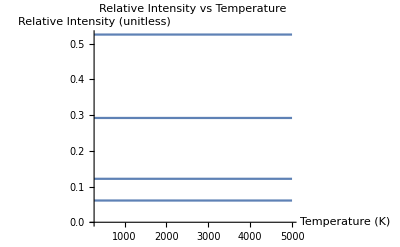

```mathematica
Plot[
relativeIntensity[temp],
{temp,273,5000},
PlotLabel-> "Relative Intensity vs Temperature",
AxesLabel->{"Temperature (K)","Relative Intensity (unitless)"},
ImageSize->Full
]
```

Plugging equation (DisplayFormulaNumbered) into Q(τ), we get

Q(τ,T)=(|∑_(m=1)^M c_m(T)e^-ⅈΔ_mτ|)^2.

Upon expanding the square, the τ dependent part of Q(τ,T) resolves to a sum of cosines with period 2π/|Δ_m-Δ_m'|. Calculating these periods, we get

```mathematica
(* Sort the Subscript[Δ, m]'s from smallest to largest first so it's easier to associate the line differences with the spectrum *)
sortedLineΔ = Sort[lineΔ];
lineΔΔ = UnitConvert[
Reap[
For[i=1, i < Length[lineΔ],i++,
For[j=i+1,j≤ Length[lineΔ],j++,
Sow[2π/Abs[sortedLineΔ[[i]]-sortedLineΔ[[j]]]];
]
]
][[2]][[1]],
"Picoseconds"
]
```

{179.101 ps,113.192 ps,101.137 ps,307.588 ps,232.335 ps,949.653 ps}

We can finally plot our signal to see what it looks like!

```mathematica
sigQ[τ_,T_]:=Re[
Total[relativeIntensity[T]*Exp[-ⅈ*lineΔTHz*τ]]
*Conjugate[Total[relativeIntensity[T]*Exp[-ⅈ*lineΔTHz*τ]]]
]

sigQUnits[τ_,T_]:=Re[
Total[relativeIntensityUnits[T]*Exp[-ⅈ*lineΔ*τ]]
*Conjugate[Total[relativeIntensityUnits[T]*Exp[-ⅈ*lineΔ*τ]]]
]
```

```mathematica
(* Slider boundaries for temperature *)
tempUnit = "Kelvins";
tempMin = 273;
tempMax = 10000;

(* Boundaries for τ *)
τUnit = "Picoseconds";
τMin = 0;
τMax = 1000;
```

```mathematica
Manipulate[
Plot[
sigQ[τ,temp],
{τ,τMin,τMax},
PlotLabel-> "Q(τ) vs τ",
AxesLabel->{"τ (picoseconds)","Q(τ,T) (unitless)"},
ImageSize->Full
],
{temp,tempMin,tempMax}
]
```

```mathematica
(* Uncomment to have Mathematica take care of units for comparison. BEWARE: very slow *)

(*Manipulate[
Plot[
sigQUnits[Quantity[τ,τUnit],Quantity[temp,tempUnit]],
{τ,τMin,τMax}
],
{temp,tempMin,tempMax}
]*)
```